```mathematica
$Assumptions= {v ∈ Reals,v>0, θ ∈ Reals, x ∈ Reals, y ∈ Reals, C1 ∈ Reals, C2 ∈ Reals, C3 ∈ Reals, d ∈ Reals, d >0, a ∈ Reals, a > 0, δ ∈ Reals, δ > 0, λ ∈ Reals, k ∈ Reals, θ ∈ Reals, ϕ ∈ Reals}
```

{v∈ℝ,v>0,θ∈ℝ,x∈ℝ,y∈ℝ,C1∈ℝ,C2∈ℝ,C3∈ℝ,d∈ℝ,d>0,a∈ℝ,a>0,δ∈ℝ,δ>0,λ∈ℝ,k∈ℝ,θ∈ℝ,ϕ∈ℝ}

## Setup

```mathematica
ω = Exp[I 2 π/3]
(*λ=1*)
q = x + I y
(*α =(2 ⅈ √3 λ^2+(3+ⅈ √3) λ^4)/(2 (1+λ^2)^2)*)
Δ =FullSimplify[1/(1 + λ^2) * (-1 - ω λ^2)]
(*Δ = d Exp[-I 2 π/3]*)
```

ⅇ^((2 ⅈ π)/3)

x+ⅈ y

-(1+(-1)^(2/3) λ^2)/(1+λ^2)

```mathematica
FullSimplify[Series[Abs[Δ]/Abs[α], {λ, 0, 3}]]
```

1/(√3 λ^2)+O[λ]^2

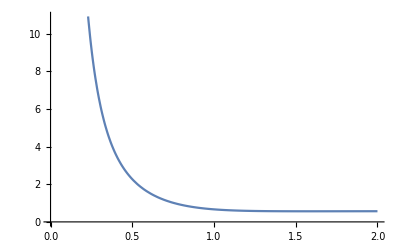

```mathematica
Plot[Abs[Δ]/Abs[α], {λ, 0, 2}]
```

## Hamiltonian

```mathematica
H = FullSimplify[1/2{{v (q + Conjugate[q]),2 Δ+ α (ω q + Conjugate[ω q]), 2 Conjugate[Δ] + Conjugate[α] (ω Conjugate[q] + q Conjugate[ω])}, {2 Conjugate[Δ] + Conjugate[α] (ω q + Conjugate[ω q]), v (Conjugate[ω] q + ω Conjugate[q]),2 Δ + α (q + Conjugate[q])}, {2 Δ + α (Conjugate[ω] q + ω Conjugate[q]), 2 Conjugate[Δ] + Conjugate[α] (q + Conjugate[q]), v (ω q + Conjugate[ω q])}}];
MatrixForm[H]
```

(v x | 1/2 ((-1-ⅈ √3) d-(x+√3 y) α) | (-1)^(2/3) d-1/2 (x-√3 y) Conjugate[α]
(-1)^(2/3) d-1/2 (x+√3 y) Conjugate[α] | -1/2 v (x-√3 y) | -(-1)^(1/3) d+x α
1/2 ((-1-ⅈ √3) d-x α+√3 y α) | (-1)^(2/3) d+x Conjugate[α] | -1/2 v (x+√3 y))

```mathematica
P = {{1, 1, 1}, {1, ω, Conjugate[ω]}, {1, Conjugate[ω], ω}};
P0 = {{0, 1, 0}, {0, 0, 1}, {1, 0, 0}};
P1 = {{0, 0, 1}, {1, 0, 0}, {0, 1, 0}};
```

```mathematica
M = FullSimplify[P.H.Inverse[P]];
MatrixForm[FullSimplify[ComplexExpand[M, {Δ, α}]]]
```

(-d | 1/2 (x-ⅈ y) (v-√3 Im[α]-Re[α]) | 1/2 (x+ⅈ y) (v+√3 Im[α]-Re[α])
1/2 (x+ⅈ y) (v-√3 Im[α]-Re[α]) | -d | 1/2 (x-ⅈ y) (v+α+Conjugate[α])
1/2 (x-ⅈ y) (v+√3 Im[α]-Re[α]) | 1/2 (x+ⅈ y) (v+α+Conjugate[α]) | 2 d)

## Identification of eigenvectors

```mathematica
v = FullSimplify[ComplexExpand[-2 Re[ω α], α]];
M = FullSimplify[ComplexExpand[M, {Δ, α}]];
MatrixForm[M]
```

(-d | 0 | √3 (x+ⅈ y) Im[α]
0 | -d | 1/2 (x-ⅈ y) (√3 Im[α]+3 Re[α])
√3 (x-ⅈ y) Im[α] | 1/2 (x+ⅈ y) (√3 Im[α]+3 Re[α]) | 2 d)

```mathematica
ev1 = FullSimplify[ComplexExpand[Normalize[{q Re[α - ω α], - Conjugate[q] Re[Conjugate[ω] α - ω α], 0}], α]];
```

```mathematica
FullSimplify[Im[Conjugate[ComplexExpand[D[ev1,x], α]].D[ev1,y]]]
```

-x y Im[1/((x^2+y^2)^2)]

```mathematica
vals  = FullSimplify[ComplexExpand[Eigenvalues[M], α]];
valm = Part[vals, 2]
valp = Part[vals, 3]
```

1/2 (d-√(9 d^2+3 (x^2+y^2) (5 Im[α]^2+2 √3 Im[α] Re[α]+3 Re[α]^2)))

1/2 (d+√(9 d^2+3 (x^2+y^2) (5 Im[α]^2+2 √3 Im[α] Re[α]+3 Re[α]^2)))

```mathematica
x=k Cos[θ]
y = k Sin[θ]
```

k Cos[θ]

k Sin[θ]

## Berry Curvature Comp

```mathematica
Clear[k]
nmzm = FullSimplify[ComplexExpand[1 + Re[Conjugate[ω] α - ω α]^2/Re[α - ω α]^2+((valm + Abs[Δ])/(k Re[α - ω α]))^2, α]];
term1 = -1/nmzm^2 * (Re[Conjugate[ω] α - ω α]/Re[α - ω α])^2 * ((2 (valm + Abs[Δ]))/(k Re[α - ω α])* D[valm, k] - 2 (valm + Abs[Δ])^2/(Re[α - ω α]^2 k^3));
term2 = -1/nmzm *((valm + Abs[Δ])/(k Re[α - ω α])) * (-((valm + Abs[Δ])/(k^2 Re[α - ω α])) + 1/(k Re[α - ω α]) * D[valm, k]) + 1/nmzm^2 * ((valm + Abs[Δ])/(k Re[α - ω α])) * 1/2 * ((valm + Abs[Δ])/(k Re[α - ω α]));
tempbcm = FullSimplify[-2/k*term1 + term2]
```

$Aborted

```mathematica
d = 1
α = Exp[I ϕ]
FullSimplify[ComplexExpand[tempbcm, α]]
```

1

ⅇ^(ⅈ ϕ)

(-20032 √3 Cos[2 ϕ]-50928 Sin[2 ϕ]+20215 √(7-Cos[2 ϕ]+√3 Sin[2 ϕ])+192 Cos[ϕ] (-75 √3+46 √(7-Cos[2 ϕ]+√3 Sin[2 ϕ]))+√(7-Cos[2 ϕ]+√3 Sin[2 ϕ]) (14438 Cos[2 ϕ]-11652 Cos[3 ϕ]-5167 Cos[4 ϕ]+2820 Cos[5 ϕ]-181 Cos[6 ϕ]+12 Cos[7 ϕ]+17 Cos[8 ϕ]-12 Cos[9 ϕ]+√3 (10272 Sin[ϕ]+9448 Sin[2 ϕ]-2004 Sin[3 ϕ]+2213 Sin[4 ϕ]-1164 Sin[5 ϕ]-351 Sin[6 ϕ]+228 Sin[7 ϕ]+Sin[8 ϕ]-4 Sin[9 ϕ]))+4 (-7964 √3+4851 √3 Cos[3 ϕ]+2540 √3 Cos[4 ϕ]-1251 √3 Cos[5 ϕ]+80 √3 Cos[6 ϕ]-9 √3 Cos[7 ϕ]-16 √3 Cos[8 ϕ]+9 √3 Cos[9 ϕ]-12600 Sin[ϕ]+2349 Sin[3 ϕ]-2694 Sin[4 ϕ]+1611 Sin[5 ϕ]+648 Sin[6 ϕ]-369 Sin[7 ϕ]-6 Sin[8 ϕ]+9 Sin[9 ϕ]))/(8 (51-14 Cos[2 ϕ]-Cos[4 ϕ]+14 √3 Sin[2 ϕ]-√3 Sin[4 ϕ])^(1/4) (-51+Cos[4 ϕ]+√3 Sin[4 ϕ]+14 √3 (51-14 Cos[2 ϕ]-Cos[4 ϕ]+14 √3 Sin[2 ϕ]-√3 Sin[4 ϕ])^(1/4)-3 √(51-14 Cos[2 ϕ]-Cos[4 ϕ]+14 √3 Sin[2 ϕ]-√3 Sin[4 ϕ])+Sin[2 ϕ] (-14 √3+6 (51-14 Cos[2 ϕ]-Cos[4 ϕ]+14 √3 Sin[2 ϕ]-√3 Sin[4 ϕ])^(1/4))-2 Cos[2 ϕ] (-7+√3 (51-14 Cos[2 ϕ]-Cos[4 ϕ]+14 √3 Sin[2 ϕ]-√3 Sin[4 ϕ])^(1/4)))^2)

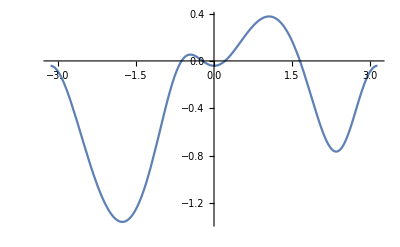

```mathematica
Plot[tempbcm, {ϕ, -Pi, Pi}]
```

## Misc Stuff

```mathematica
evm = FullSimplify[ComplexExpand[Normalize[{q/Conjugate[q] Re[Conjugate[ω] α - ω α]/Re[α - ω α], 1, (valm + Abs[Δ])/(Conjugate[q]Re[α - ω α])}], α]]
evp = FullSimplify[ComplexExpand[Normalize[{q/Conjugate[q] Re[Conjugate[ω] α - ω α]/Re[α - ω α], 1, (valp + Abs[Δ])/(Conjugate[q]Re[α - ω α])}], α]]
```

$Aborted

$Aborted

```mathematica
Clear[x,y]
tempm = FullSimplify[ComplexExpand[-2 * Im[Conjugate[D[evm, x].D[evm,y]]]]]
```

(y^2 (590490 x^14+6561 x^12 (396 y^2+49 (6+√2 √(2+9 x^2+9 y^2)))+9 y^6 (2+9 y^2) (32 (2+√2 √(2+9 x^2+9 y^2))+144 y^2 (3+√2 √(2+9 x^2+9 y^2))+81 y^4 (8+√2 √(2+9 x^2+9 y^2)))+1458 x^10 (1054+291 √2 √(2+9 x^2+9 y^2)+9 y^2 (466+315 y^2+79 √2 √(2+9 x^2+9 y^2)))-18 x^6 (-32 (130+57 √2 √(2+9 x^2+9 y^2))-36 y^2 (842+309 √2 √(2+9 x^2+9 y^2))+81 y^4 (-374+405 y^4-117 √2 √(2+9 x^2+9 y^2)+18 y^2 (64+7 √2 √(2+9 x^2+9 y^2))))-2 x^2 y^2 (2+9 y^2) (512 (2+√2 √(2+9 x^2+9 y^2))+144 y^2 (90+37 √2 √(2+9 x^2+9 y^2))+81 y^4 (644+194 √2 √(2+9 x^2+9 y^2)+9 y^2 (100+27 y^2+17 √2 √(2+9 x^2+9 y^2))))+81 x^8 (8 (782+285 √2 √(2+9 x^2+9 y^2))+9 y^2 (4444+1236 √2 √(2+9 x^2+9 y^2)+9 y^2 (796+360 y^2+143 √2 √(2+9 x^2+9 y^2))))-x^4 (-2048 (2+√2 √(2+9 x^2+9 y^2))+27 (-64 y^2 (2+√2 √(2+9 x^2+9 y^2))+24 y^4 (642+229 √2 √(2+9 x^2+9 y^2))+27 y^6 (3340+894 √2 √(2+9 x^2+9 y^2)+9 y^2 (634+180 y^2+97 √2 √(2+9 x^2+9 y^2)))))))/((x^2+y^2)^4 (2+9 x^2+9 y^2)^(3/2) (√2+√(2+9 x^2+9 y^2)) (2+9 x^2+9 y^2+√2 √(2+9 x^2+9 y^2))^3)

## Perturbation (v_F)

```mathematica
y=0
```

0

```mathematica
δV = FullSimplify[ δ {{0, Conjugate[q], q}, {q, 0, Conjugate[q]}, {Conjugate[q], q, 0}}]
```

{{0,x δ,x δ},{x δ,0,x δ},{x δ,x δ,0}}

```mathematica
E0 = FullSimplify[Part[vals, 1] + Conjugate[ev1].δV.ev1]
(*Em = FullSimplify[valm + Conjugate[evm].δV.evm]
Ep = FullSimplify[valp + Conjugate[evp].δV.evp]*)
```

-1/2-x δ

```mathematica
FullSimplify[Series[E0 - Em, {x, 0, 5}]]
```

(-1/2-Em)-(δ x)/2+O[x]^6

```mathematica
δ=0.2
```

0.2

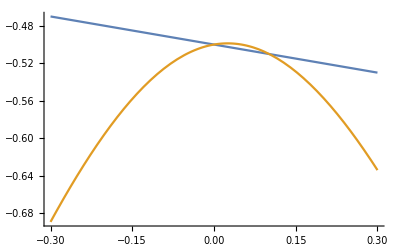

```mathematica
Plot[{E0, Em}, {x, -0.3, 0.3}]
```

## Perturbation (q)

```mathematica
δV = FullSimplify[1/2 δ {{0, Conjugate[q] * (v + ω α + Conjugate[ω α]), q * (v + Conjugate[ω] α + ω Conjugate[α])}, {q * (v + ω α + Conjugate[ω α]), 0, Conjugate[q] (v + α + Conjugate[α])}, {Conjugate[q]* (v + Conjugate[ω] α + ω Conjugate[α]), q*(v + α + Conjugate[α]), 0}}]
```

{{0,0,9/8 (x+ⅈ y) δ},{0,0,9/8 (x-ⅈ y) δ},{9/8 (x-ⅈ y) δ,9/8 (x+ⅈ y) δ,0}}

```mathematica
E0 = FullSimplify[Part[vals, 1] + Conjugate[ev1].δV.ev1]
(*Em = FullSimplify[valm + Conjugate[evm].δV.evm]*)
```

-1/2

(-27 √2 (x^2+y^2)^(3/2) δ-(x-ⅈ y) (-8 √(2+9 x^2+9 y^2)+27 √2 x^2 (4+3 δ)+3 √2 (8+9 y^2 (4+3 δ))) Conjugate[Sign[x-ⅈ y]])/(32 √((x^2+y^2) (2+9 x^2+9 y^2)) Conjugate[Sign[x-ⅈ y]] Sign[x-ⅈ y])

```mathematica
(*E12 =  FullSimplify[ComplexExpand[Abs[Conjugate[ev1].δV.evm]^2/(valm-Part[vals,1])+Abs[Conjugate[evp].δV.evm]^2/(valm-valp)],Assumptions->ϕ ∈ Reals]*)
```

-(27 δ^2)/(44 √22)

0

0.001

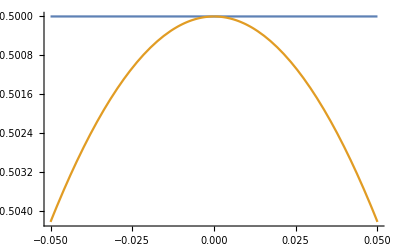

```mathematica
y=0
δ = 0.001
Plot[{E0, Em}, {x, -0.05, 0.05}]
```

## Perturbation (λ)

```mathematica
β=0
Clear[γ]
(*γ = 0
Clear[β]*)
```

0

```mathematica
δV = FullSimplify[{{2 Re[β], Conjugate[q] Re[ω γ], q Re[Conjugate[ω] γ]}, {q Re[ω γ], 2 Re[Conjugate[ω] β], Conjugate[q] Re[γ]}, {Conjugate[q] Re[Conjugate[ω] γ],q Re[γ], 2 Re[ω β]}}]
```

{{0,(x-ⅈ y) Re[(-1)^(2/3) γ],-((x+ⅈ y) Re[(-1)^(1/3) γ])},{(x+ⅈ y) Re[(-1)^(2/3) γ],0,(x-ⅈ y) Re[γ]},{-((x-ⅈ y) Re[(-1)^(1/3) γ]),(x+ⅈ y) Re[γ],0}}

```mathematica
Clear[y, γ, x]
```

```mathematica
y=0
```

0

```mathematica
E0 =  FullSimplify[ComplexExpand[Part[vals, 1] + Conjugate[ev1].δV.ev1, γ]]
Em =  Simplify[ComplexExpand[valm + Conjugate[evm].δV.evm, γ]]
```

-(x^2+y^2-x (x^2-3 y^2) (√3 Im[γ]+Re[γ]))/(2 (x^2+y^2))

$Aborted

```mathematica
FullSimplify[Series[E0, {x, 0, 2}]]
```

-1/2-3/2 (√3 Im[γ]+Re[γ]) x+O[x]^3

```mathematica
Clear[x, y]
```

```mathematica
(*E2 =  Abs[Conjugate[evm].δV.ev1]^2/(Part[vals,1]-valm)+Abs[Conjugate[evp].δV.ev1]^2/(Part[vals,1]-valp)*)
```

ⅇ^((ⅈ π)/4)

a

0

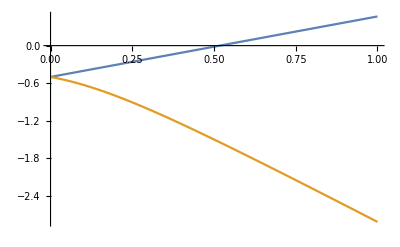

ⅇ^((ⅈ π)/4)

(√3 a)/2

a/2

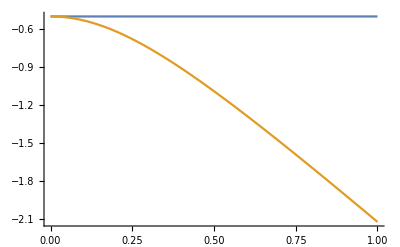

ⅇ^((ⅈ π)/4)

a/2

(√3 a)/2

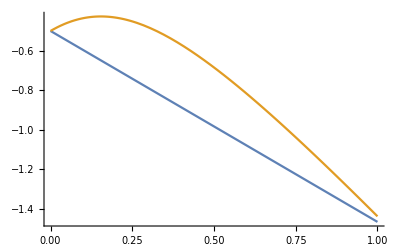

ⅇ^((ⅈ π)/4)

0

a

-Graphics-

ⅇ^((ⅈ π)/4)

-a/2

(√3 a)/2

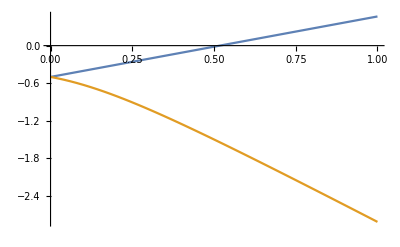

ⅇ^((ⅈ π)/4)

-(√3 a)/2

a/2

-Graphics-

```mathematica
(*β = 0.1 * Exp[I π*0]*)
γ = Exp[I π/4]
x = a * Cos[0]
y = a * Sin[0]
Plot[{E0, Em}, {a, 0, 1}]
γ = Exp[I π/4]
x = a * Cos[π/6]
y = a * Sin[π/6]
Plot[{E0, Em}, {a, 0, 1}]
γ = Exp[I π/4]
x = a * Cos[(2 π)/6]
y = a * Sin[(2 π)/6]
Plot[{E0, Em}, {a, 0, 1}]
γ = Exp[I π/4]
x = a * Cos[(3 π)/6]
y = a * Sin[(3 π)/6]
Plot[{E0, Em}, {a, 0, 1}]
γ = Exp[I π/4]
x = a * Cos[(4 π)/6]
y = a * Sin[(4 π)/6]
Plot[{E0, Em}, {a, 0, 1}]
γ = Exp[I π/4]
x = a * Cos[(5 π)/6]
y = a * Sin[(5 π)/6]
Plot[{E0, Em}, {a, 0, 1}]
```

ⅇ^((ⅈ π)/4)

a Cos[π/7]

a Sin[π/7]

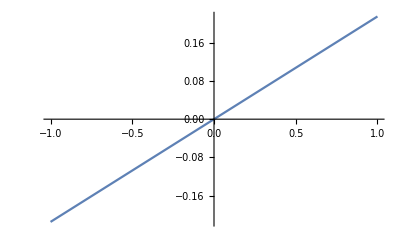

```mathematica
γ = Exp[I π/4]
x = a * Cos[π/7]
y = a * Sin[π/7]
Plot[{E0}, {a, -1, 1}]
```

```mathematica
γ = Exp[I π/4]
x = a * Cos[(3*π)/7]
y = a * Sin[(3*π)/7]
Plot[{E0}, {a, -1, 1}]
```

## Shit

```mathematica
FullSimplify[ComplexExpand[ω α + Conjugate[ω α], α]]
```

-√3 Im[α]-Re[α]

```mathematica
FullSimplify[ComplexExpand[Conjugate[ω] α + ω Conjugate[α], α]]
```

√3 Im[α]-Re[α]

```mathematica
Clear[Δ]
```

```mathematica
v =- 2Re[α]
MatrixForm[FullSimplify[ComplexExpand[M]]]
```

-2 Re[ⅇ^(ⅈ θ)]

(2 d | 0 | √3 (x+ⅈ y) Sin[θ]
0 | -d | 1/2 (x-ⅈ y) (3 Cos[θ]+√3 Sin[θ])
√3 (x-ⅈ y) Sin[θ] | 1/2 (x+ⅈ y) (3 Cos[θ]+√3 Sin[θ]) | -d)

```mathematica
FullSimplify[Eigenvalues[FullSimplify[ComplexExpand[M]]]]
```

{-d,1/2 (d-√(9 d^2+12 (x^2+y^2)+6 (x^2+y^2) Cos[2 θ])),1/2 (d+√(9 d^2+12 (x^2+y^2)+6 (x^2+y^2) Cos[2 θ]))}

```mathematica
temp = FullSimplify[Normalize[Part[Eigenvectors[FullSimplify[ComplexExpand[M]]],1]]]
```

{0,((x+ⅈ y) (-3 Cos[θ]+√3 Sin[θ]))/(√6 (x-ⅈ y) (√3 Cos[θ]+Sin[θ]) √(1/(1+(√3 Sin[2 θ])/(2+Cos[2 θ])))),Abs[3 Cos[θ]+√3 Sin[θ]]/(√6 √(2+Cos[2 θ]))}

```mathematica
FullSimplify[ComplexExpand[-2*Im[Conjugate[D[temp,x]].D[temp,y]]]]
```

0

```mathematica
A1 = 1
A3 = FullSimplify[ComplexExpand[(-(x - I y) (v + 2 Cos[θ + 2 π/3]))/((x + I y) (v + 2 Cos[θ]))]]
A5 = FullSimplify[ComplexExpand[((x + I y) (v + 2 Cos[θ - π/3]))/((x - I y) (v + 2 Cos[θ]))]]
```

1

((x-ⅈ y) (-v+2 Sin[π/6+θ]))/((x+ⅈ y) (v+2 Cos[θ]))

((x+ⅈ y) (v+2 Sin[π/6+θ]))/((x-ⅈ y) (v+2 Cos[θ]))

```mathematica
nmz = FullSimplify[1/Sqrt[Abs[A1]^2 + Abs[A3]^2 + Abs[A5]^2]]
```

Abs[v+2 Cos[θ]]/(√(6+3 v^2+4 v Cos[θ]+2 √3 Sin[2 θ]))

```mathematica
dxA3 = FullSimplify[D[nmz * A3, x]]
dyA3 = FullSimplify[D[nmz * A3, y]]
dxA5 = FullSimplify[D[nmz * A5, x]]
dyA5 = FullSimplify[D[nmz * A5, y]]
```

-(2 ⅈ y (v-2 Sin[π/6+θ]))/((x+ⅈ y)^2 Sign[v+2 Cos[θ]] √(6+3 v^2+4 v Cos[θ]+2 √3 Sin[2 θ]))

(2 ⅈ x (v-2 Sin[π/6+θ]))/((x+ⅈ y)^2 Sign[v+2 Cos[θ]] √(6+3 v^2+4 v Cos[θ]+2 √3 Sin[2 θ]))

(2 ⅈ y (v+2 Sin[π/6+θ]))/((ⅈ x+y)^2 Sign[v+2 Cos[θ]] √(6+3 v^2+4 v Cos[θ]+2 √3 Sin[2 θ]))

(2 ⅈ x (v+2 Sin[π/6+θ]))/((x-ⅈ y)^2 Sign[v+2 Cos[θ]] √(6+3 v^2+4 v Cos[θ]+2 √3 Sin[2 θ]))

```mathematica
FullSimplify[ComplexExpand[-2 * Im[Conjugate[dxA3] * dyA3 + Conjugate[dxA5] * dyA5]]]
```

0

```mathematica
v0 = FullSimplify[nmz * {A1, A3,A5}]
```

{Abs[v+2 Cos[θ]]/(√(6+3 v^2+4 v Cos[θ]+2 √3 Sin[2 θ])),((x-ⅈ y) (-v+2 Sin[π/6+θ]))/((x+ⅈ y) Sign[v+2 Cos[θ]] √(6+3 v^2+4 v Cos[θ]+2 √3 Sin[2 θ])),((x+ⅈ y) (v+2 Sin[π/6+θ]))/((x-ⅈ y) Sign[v+2 Cos[θ]] √(6+3 v^2+4 v Cos[θ]+2 √3 Sin[2 θ]))}

```mathematica
e1 = {1, 0, 0}
v1t = FullSimplify[e1 - (Conjugate[nmz * {A1, A3, A5}].e1) * nmz * {A1, A3, A5}]
nmz2 = FullSimplify[Conjugate[v1t].v1t]
v1 = FullSimplify[ComplexExpand[1/Sqrt[nmz2] * v1t]]
```

{1,0,0}

{(2 (2+v^2-Cos[2 θ]+√3 Sin[2 θ]))/(3 (2+v^2)+4 Cos[θ] (v+√3 Sin[θ])),((x-ⅈ y) (v+2 Cos[θ]) (v-2 Sin[π/6+θ]))/((x+ⅈ y) (3 (2+v^2)+4 Cos[θ] (v+√3 Sin[θ]))),-((x+ⅈ y) (v+2 Cos[θ]) (v+2 Sin[π/6+θ]))/((x-ⅈ y) (3 (2+v^2)+4 Cos[θ] (v+√3 Sin[θ])))}

(4 (2+v^2-Cos[2 θ]+√3 Sin[2 θ])^2+(v+2 Cos[θ])^2 (v-2 Sin[π/6+θ])^2+(v+2 Cos[θ])^2 (v+2 Sin[π/6+θ])^2)/(3 (2+v^2)+4 Cos[θ] (v+√3 Sin[θ]))^2

{(√2 (120+144 v^2+62 v^4+9 v^6+12 v (8+7 v^2+2 v^4) Cos[θ]-(39+28 v^2+v^4) Cos[2 θ]-48 Cos[4 θ]+3 Cos[6 θ]+93 √3 Sin[2 θ]+v (-12 (3+v^2) Cos[3 θ]-28 v Cos[4 θ]-12 Cos[5 θ]+√3 (92 v+21 v^3+8 (9+5 v^2) Cos[θ]-4 v Cos[2 θ]-8 Cos[3 θ]) Sin[2 θ])-12 √3 Sin[4 θ]-3 √3 Sin[6 θ]))/((3 (2+v^2)+4 Cos[θ] (v+√3 Sin[θ]))^2 √(3 (5+4 v^2+v^4)-3 (2+v^2) Cos[2 θ]-2 v Cos[3 θ]-3 Cos[4 θ]+5 √3 (2+v^2) Sin[2 θ]+2 v Cos[θ] (3+2 v^2+2 √3 Sin[2 θ])-√3 Sin[4 θ])),((x-ⅈ y) (v+2 Cos[θ]) (42+44 v^2+9 v^4+24 v (2+v^2) Cos[θ]+8 v^2 Cos[2 θ]-6 Cos[4 θ]+4 √3 (6+3 v^2+4 v Cos[θ]) Sin[2 θ]) (v-2 Sin[π/6+θ]))/((x+ⅈ y) (3 (2+v^2)+4 Cos[θ] (v+√3 Sin[θ]))^2 √(6 (5+4 v^2+v^4)+4 v (3+2 v^2) Cos[θ]-6 (2+v^2) Cos[2 θ]-6 Cos[4 θ]+4 v Cos[θ] (1-2 Cos[2 θ]+√3 (5 v+4 Cos[θ]) Sin[θ])+20 √3 Sin[2 θ]-2 √3 Sin[4 θ])),-(((x+ⅈ y) (v+2 Cos[θ]) (42+44 v^2+9 v^4+24 v (2+v^2) Cos[θ]+8 v^2 Cos[2 θ]-6 Cos[4 θ]+4 √3 (6+3 v^2+4 v Cos[θ]) Sin[2 θ]) (v+2 Sin[π/6+θ]))/((x-ⅈ y) (3 (2+v^2)+4 Cos[θ] (v+√3 Sin[θ]))^2 √(6 (5+4 v^2+v^4)+4 v (3+2 v^2) Cos[θ]-6 (2+v^2) Cos[2 θ]-6 Cos[4 θ]+4 v Cos[θ] (1-2 Cos[2 θ]+√3 (5 v+4 Cos[θ]) Sin[θ])+20 √3 Sin[2 θ]-2 √3 Sin[4 θ])))}

## Some Calcs

```mathematica
q=x + I y
```

x+ⅈ y

```mathematica
v1Hv1 = FullSimplify[ComplexExpand[Conjugate[q] C3 Conjugate[q] C1/(q C2) + q C3 q C1/(Conjugate[q] C2), q]]
v1Hv2 = FullSimplify[ComplexExpand[Conjugate[q] C3 ((- Conjugate[q])/q C1 C2 C3^2) Conjugate[q] C1/(q C2) + q C3 C2^2 C3^2 + Conjugate[q] C2 q/Conjugate[q] C3 C2 (C1^2+C2^2) + q C1 q/Conjugate[q] C3 C2 (C1^2 + C2^2) Conjugate[q] C1/(q C2), q]]
v2Hv1 = FullSimplify[ComplexExpand[Conjugate[v1Hv2], q]]
v2Hv2 = FullSimplify[ComplexExpand[Conjugate[q] C3 ((-Conjugate[q])/q C1 C2 C3^2) C2^2 C3^2 + q C3 C2^2 C3^2 (-q/Conjugate[q] C1 C2 C3^2) + q C1 C2^2 C3^2 (q/Conjugate[q] C3 C2 (C1^2+ C2^2)) + Conjugate[q] C1 C2^2 C3^2 (Conjugate[q]/q C3 C2 (C1^2 + C2^2)) + Conjugate[q] C2 q/Conjugate[q] C3 C2 (C1^2 + C2^2) (-q/Conjugate[q] C1 C2 C3^2) + q C2 Conjugate[q]/q C3 C2 (C1^2 + C2^2) ((-Conjugate[q])/q C1 C2 C3^2), q]]
```

(2 C1 C3 x (x^2-3 y^2))/(C2 (x^2+y^2))

(C1^2 C3 (-C3^2 (x-ⅈ y)^3+2 C2^2 (x+ⅈ y)^3))/(x+ⅈ y)^2+C1^4 C3 (x+ⅈ y)+C2^2 C3 (C2^2+C3^2) (x+ⅈ y)

(C1^2 C3 (2 C2^2 (x-ⅈ y)^3-C3^2 (x+ⅈ y)^3))/(x-ⅈ y)^2+C1^4 C3 (x-ⅈ y)+C2^2 C3 (C2^2+C3^2) (x-ⅈ y)

-(2 C1 C2^3 C3^5 x (x^2-3 y^2))/(x^2+y^2)

```mathematica
N1 = FullSimplify[Sqrt[C1^2/C2^2+1]]
N2 = FullSimplify[Sqrt[C2^4 C3^4 + C1^2 C2^2 C3^4 + C2^2 C3^2 (C1^2 + C2^2)^2]]
```

√(1+C1^2/C2^2)

√((C1^2+C2^2) (C1^2+C2^2+C3^2)) Abs[C2] Abs[C3]

```mathematica
Ham =FullSimplify[ {{1/N1^2 v1Hv1, 1/(N1 N2)v1Hv2}, {1/(N1 N2)v2Hv1, 1/N2^2 v2Hv2}}]
```

{{(2 C1 C2 C3 x (x^2-3 y^2))/((C1^2+C2^2) (x^2+y^2)),((C1^2 C3 (-C3^2 (x-ⅈ y)^3+2 C2^2 (x+ⅈ y)^3))/(x+ⅈ y)^2+C1^4 C3 (x+ⅈ y)+C2^2 C3 (C2^2+C3^2) (x+ⅈ y))/((C1^2+C2^2) √(C3^2 (C1^2+C2^2+C3^2)))},{((C1^2 C3 (2 C2^2 (x-ⅈ y)^3-C3^2 (x+ⅈ y)^3))/(x-ⅈ y)^2+C1^4 C3 (x-ⅈ y)+C2^2 C3 (C2^2+C3^2) (x-ⅈ y))/((C1^2+C2^2) √(C3^2 (C1^2+C2^2+C3^2))),-(2 C1 C2 C3^3 x (x^2-3 y^2))/((C1^2+C2^2) (C1^2+C2^2+C3^2) (x^2+y^2))}}

```mathematica
FullSimplify[Eigenvectors[Ham]]
```

{{((x-ⅈ y) (-((C1^2+C2^2) √(C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))))+C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3]))/(√(C1^2+C2^2+C3^2) (C1^2 (2 C2^2 (x-ⅈ y)^3-C3^2 (x+ⅈ y)^3)+C1^4 (x-ⅈ y)^3+C2^2 (C2^2+C3^2) (x-ⅈ y)^3) (x+ⅈ y)),1},{((x-ⅈ y) ((C1^2+C2^2) √(C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6)))+C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3]))/(√(C1^2+C2^2+C3^2) (C1^2 (2 C2^2 (x-ⅈ y)^3-C3^2 (x+ⅈ y)^3)+C1^4 (x-ⅈ y)^3+C2^2 (C2^2+C3^2) (x-ⅈ y)^3) (x+ⅈ y)),1}}

```mathematica
λ1vec = FullSimplify[{((x-ⅈ y) (-((C1^2+C2^2) √(C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))))+C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3]))/(√(C1^2+C2^2+C3^2) (C1^2 (2 C2^2 (x-ⅈ y)^3-C3^2 (x+ⅈ y)^3)+C1^4 (x-ⅈ y)^3+C2^2 (C2^2+C3^2) (x-ⅈ y)^3) (x+ⅈ y)),1}]
```

{((x-ⅈ y) (-((C1^2+C2^2) √(C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))))+C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3]))/(√(C1^2+C2^2+C3^2) (C1^2 (2 C2^2 (x-ⅈ y)^3-C3^2 (x+ⅈ y)^3)+C1^4 (x-ⅈ y)^3+C2^2 (C2^2+C3^2) (x-ⅈ y)^3) (x+ⅈ y)),1}

```mathematica
term1 = FullSimplify[((x-ⅈ y) (-((C1^2+C2^2) √(C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))))+C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3]))/(√(C1^2+C2^2+C3^2) (C1^2 (2 C2^2 (x-ⅈ y)^3-C3^2 (x+ⅈ y)^3)+C1^4 (x-ⅈ y)^3+C2^2 (C2^2+C3^2) (x-ⅈ y)^3) (x+ⅈ y))]
term2 = 1
```

((x-ⅈ y) (-((C1^2+C2^2) √(C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))))+C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3]))/(√(C1^2+C2^2+C3^2) (C1^2 (2 C2^2 (x-ⅈ y)^3-C3^2 (x+ⅈ y)^3)+C1^4 (x-ⅈ y)^3+C2^2 (C2^2+C3^2) (x-ⅈ y)^3) (x+ⅈ y))

1

```mathematica
nmz = FullSimplify[ComplexExpand[Conjugate[λ1vec].λ1vec]]
```

((C1^2+C2^2) ((C1^2+C2^2) (C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6)))+(C1^2+C2^2) Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]-2 C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3] √Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))] Cos[1/2 Arg[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]]))/((C1^2+C2^2+C3^2) (C1^8 (x^2+y^2)^3+C2^4 (C2^2+C3^2)^2 (x^2+y^2)^3+C1^4 (6 C2^4 (x^2+y^2)^3+C3^4 (x^2+y^2)^3-2 C2^2 C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+2 C1^6 (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))+2 C1^2 C2^2 (C2^2+C3^2) (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))))

## Basis Berry Curvature

```mathematica
vec1 =FullSimplify[ 1/N1 {q C1/(Conjugate[q] C2), 1, 0}]
vec2 =FullSimplify[ 1/N2 {C2^2 C3^2, (-Conjugate[q])/q C1 C2 C3^2, q/Conjugate[q] C3 C2 (C1^2 + C2^2)}]
```

{(C1 (x+ⅈ y))/(√(C1^2+C2^2) (x-ⅈ y) Sign[C2]),Abs[C2]/(√(C1^2+C2^2)),0}

{Abs[C2 C3]/(√((C1^2+C2^2) (C1^2+C2^2+C3^2))),-(C1 C2 (x-ⅈ y) Abs[C3])/(√((C1^2+C2^2) (C1^2+C2^2+C3^2)) (x+ⅈ y) Abs[C2]),(√((C1^2+C2^2)/(C1^2+C2^2+C3^2)) (x+ⅈ y) Sign[C2] Sign[C3])/(x-ⅈ y)}

```mathematica
dxvec1 = FullSimplify[D[vec1, x]]
dyvec1 = FullSimplify[D[vec1, y]]
dxvec2 = FullSimplify[D[vec2, x]]
dyvec2 = FullSimplify[D[vec2, y]]
```

{(2 ⅈ C1 y)/(√(C1^2+C2^2) (ⅈ x+y)^2 Sign[C2]),0,0}

{(2 ⅈ C1 x)/(√(C1^2+C2^2) (x-ⅈ y)^2 Sign[C2]),0,0}

{0,-(2 ⅈ C1 C2 y Abs[C3])/(√((C1^2+C2^2) (C1^2+C2^2+C3^2)) (x+ⅈ y)^2 Abs[C2]),(2 ⅈ √((C1^2+C2^2)/(C1^2+C2^2+C3^2)) y Sign[C2] Sign[C3])/(ⅈ x+y)^2}

{0,(2 ⅈ C1 C2 x Abs[C3])/(√((C1^2+C2^2) (C1^2+C2^2+C3^2)) (x+ⅈ y)^2 Abs[C2]),(2 ⅈ √((C1^2+C2^2)/(C1^2+C2^2+C3^2)) x Sign[C2] Sign[C3])/(x-ⅈ y)^2}

```mathematica
FullSimplify[ComplexExpand[Im[Conjugate[dxvec1].dyvec1]]]
```

0

```mathematica
FullSimplify[ComplexExpand[Im[Conjugate[dxvec2].dyvec2]]]
```

0

```mathematica
C1 = FullSimplify[v + 2 Cos[θ + 2 π/3]]
C2 = FullSimplify[v + 2 Cos[θ]]
C3 = FullSimplify[v + 2 Cos[θ - π/3]]
```

v-2 Sin[π/6+θ]

v+2 Cos[θ]

v+2 Sin[π/6+θ]

```mathematica
x=1
y=0
```

1

0

```mathematica
θ=π/2
```

π/2

```mathematica
Clear[v]
```

```mathematica
v =N[FullSimplify[ 1/2 + 1/2 Abs[Cos[3/2 θ]]^(9/10)]]
```

0.866021

```mathematica
Clear[θ]
```

```mathematica
N[Sqrt[3]/2]
```

0.866025

```mathematica
FullSimplify[MatrixForm[Ham]]
```

((2 v (-3+v^2))/(3+2 v (-√3+v)) | (v (-36+v (21 √3+v (15-2 √3 v+4 v^2))))/(√3 √((2+v^2) (3+2 √3 v+v^2)) (3+2 v (-√3+v)))
(v (-36+v (21 √3+v (15-2 √3 v+4 v^2))))/(√3 √((2+v^2) (3+2 √3 v+v^2)) (3+2 v (-√3+v))) | -(2 v (-√3+v) (√3+v)^3)/(3 (2+v^2) (3+2 v (-√3+v))))

```mathematica
NSolve[(4+√3+v (√2-√6+2 v))==0, v]
```

{{v→0.258819-1.67303 ⅈ},{v→0.258819+1.67303 ⅈ}}

```mathematica
θ=π/2
```

π/2

```mathematica
FullSimplify[v1Hv1]
```

((-22+2^(1/8)+2 2^(9/16)) x (x^2-3 y^2))/((2+2^(9/16)) (x^2+y^2))

```mathematica
FullSimplify[
```

```mathematica
FullSimplify[Eigenvectors[Ham]]
```

{{-(x+ⅈ y)/(√(x^2+y^2)),1},{(x+ⅈ y)/(√(x^2+y^2)),1}}

```mathematica
Clear[θ]
```

```mathematica
Clear[x,y]
```

```mathematica
FullSimplify[Solve[v1Hv2==0, v]]
```

{}

## Stuff

```mathematica
Clear[x,y]
```

```mathematica
wholeterm1x = D[1/Sqrt[nmz] * term1, x] * vec1 + D[1/Sqrt[nmz]* term2, x] * vec2
wholeterm1y =  D[1/Sqrt[nmz] * term1, y] * vec1 + D[1/Sqrt[nmz]* term2, y] * vec2
wholeterm2x = 1/Sqrt[nmz] * term1 * dxvec1 + 1/Sqrt[nmz] * term2 * dxvec2
wholeterm2y = 1/Sqrt[nmz] * term1 * dyvec1 + 1/Sqrt[nmz] * term2 * dyvec2
```

{-(Abs[C2 C3] (-((C1^2+C2^2) (1) (1))/((C1^2+C2^2+C3^2) (1)^2)+1))/(2 √((C1^2+C2^2) (C1^2+C2^2+C3^2)) (((1) 1)/((1) 1))^(3/2))+(C1 (x+ⅈ y) (1))/(√(C1^2+C2^2) (x-ⅈ y) Sign[C2]),(C1 4)/(2 3 1)+1,-1/(2 (x-ⅈ y) (1)^(3/2))}
 |  |  |  |

{-(Abs[C2 C3] (-((C1^2+C2^2) (1) (1))/((C1^2+C2^2+C3^2) (1)^2)+1))/(2 √((C1^2+C2^2) (C1^2+C2^2+C3^2)) (((1) 1)/((1) 1))^(3/2))+(C1 (x+ⅈ y) (1))/(√(C1^2+C2^2) (x-ⅈ y) Sign[C2]),(C1 4)/(2 3 1)+1,-1/(2 (x-ⅈ y) (1)^(3/2))}
 |  |  |  |

{(2 ⅈ C1 (x-ⅈ y) y (-((C1^2+C2^2) √(C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))))+C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3]))/(√(C1^2+C2^2) √(C1^2+C2^2+C3^2) (C1^2 (2 C2^2 (x-ⅈ y)^3-C3^2 (x+ⅈ y)^3)+C1^4 (x-ⅈ y)^3+C2^2 (C2^2+C3^2) (x-ⅈ y)^3) (x+ⅈ y) (ⅈ x+y)^2 √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6)))+(C1^2+C2^2) Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]-2 C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3] √Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))] Cos[1/2 Arg[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]]))/((C1^2+C2^2+C3^2) (C1^8 (x^2+y^2)^3+C2^4 (C2^2+C3^2)^2 (x^2+y^2)^3+C1^4 (6 C2^4 (x^2+y^2)^3+C3^4 (x^2+y^2)^3-2 C2^2 C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+2 C1^6 (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))+2 C1^2 C2^2 (C2^2+C3^2) (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))))) Sign[C2]),-((2 ⅈ C1 C2 y Abs[C3])/(√((C1^2+C2^2) (C1^2+C2^2+C3^2)) (x+ⅈ y)^2 Abs[C2] √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6)))+(C1^2+C2^2) Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]-2 C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3] √Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))] Cos[1/2 Arg[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]]))/((C1^2+C2^2+C3^2) (C1^8 (x^2+y^2)^3+C2^4 (C2^2+C3^2)^2 (x^2+y^2)^3+C1^4 (6 C2^4 (x^2+y^2)^3+C3^4 (x^2+y^2)^3-2 C2^2 C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+2 C1^6 (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))+2 C1^2 C2^2 (C2^2+C3^2) (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))))))),(2 ⅈ √((C1^2+C2^2)/(C1^2+C2^2+C3^2)) y Sign[C2] Sign[C3])/((ⅈ x+y)^2 √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6)))+(C1^2+C2^2) Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]-2 C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3] √Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))] Cos[1/2 Arg[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]]))/((C1^2+C2^2+C3^2) (C1^8 (x^2+y^2)^3+C2^4 (C2^2+C3^2)^2 (x^2+y^2)^3+C1^4 (6 C2^4 (x^2+y^2)^3+C3^4 (x^2+y^2)^3-2 C2^2 C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+2 C1^6 (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))+2 C1^2 C2^2 (C2^2+C3^2) (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))))))}

{(2 ⅈ C1 x (-((C1^2+C2^2) √(C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))))+C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3]))/(√(C1^2+C2^2) √(C1^2+C2^2+C3^2) (C1^2 (2 C2^2 (x-ⅈ y)^3-C3^2 (x+ⅈ y)^3)+C1^4 (x-ⅈ y)^3+C2^2 (C2^2+C3^2) (x-ⅈ y)^3) (x-ⅈ y) (x+ⅈ y) √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6)))+(C1^2+C2^2) Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]-2 C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3] √Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))] Cos[1/2 Arg[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]]))/((C1^2+C2^2+C3^2) (C1^8 (x^2+y^2)^3+C2^4 (C2^2+C3^2)^2 (x^2+y^2)^3+C1^4 (6 C2^4 (x^2+y^2)^3+C3^4 (x^2+y^2)^3-2 C2^2 C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+2 C1^6 (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))+2 C1^2 C2^2 (C2^2+C3^2) (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))))) Sign[C2]),(2 ⅈ C1 C2 x Abs[C3])/(√((C1^2+C2^2) (C1^2+C2^2+C3^2)) (x+ⅈ y)^2 Abs[C2] √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6)))+(C1^2+C2^2) Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]-2 C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3] √Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))] Cos[1/2 Arg[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]]))/((C1^2+C2^2+C3^2) (C1^8 (x^2+y^2)^3+C2^4 (C2^2+C3^2)^2 (x^2+y^2)^3+C1^4 (6 C2^4 (x^2+y^2)^3+C3^4 (x^2+y^2)^3-2 C2^2 C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+2 C1^6 (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))+2 C1^2 C2^2 (C2^2+C3^2) (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6)))))),(2 ⅈ √((C1^2+C2^2)/(C1^2+C2^2+C3^2)) x Sign[C2] Sign[C3])/((x-ⅈ y)^2 √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6)))+(C1^2+C2^2) Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]-2 C1 C2 (C1^2+C2^2+2 C3^2) x (x^2-3 y^2) Abs[C3] √Abs[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))] Cos[1/2 Arg[C1^6 (x^2+y^2)^3+(C2^2+C3^2)^3 (x^2+y^2)^3+C1^4 (3 C2^2 (x^2+y^2)^3-C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+C1^2 (3 C2^4 (x^2+y^2)^3-C3^4 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6)+3 C2^2 C3^2 (x^6+12 x^4 y^2-3 x^2 y^4+2 y^6))]]))/((C1^2+C2^2+C3^2) (C1^8 (x^2+y^2)^3+C2^4 (C2^2+C3^2)^2 (x^2+y^2)^3+C1^4 (6 C2^4 (x^2+y^2)^3+C3^4 (x^2+y^2)^3-2 C2^2 C3^2 (x^6-33 x^4 y^2+27 x^2 y^4-3 y^6))+2 C1^6 (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))+2 C1^2 C2^2 (C2^2+C3^2) (2 C2^2 (x^2+y^2)^3+C3^2 (-x^6+15 x^4 y^2-15 x^2 y^4+y^6))))))}

```mathematica
x = 1
y = 0
```

1

0

```mathematica
vecdx = wholeterm1x + wholeterm2x
vecdy = wholeterm1y + wholeterm2y
```

{-((Abs[C2 C3] (-(((C1^2+C2^2) (6 C1^8+2 C1^6 (12 C2^2-6 C3^2)+2 C1^2 C2^2 (12 C2^2-6 C3^2) (C2^2+C3^2)+6 C2^4 (C2^2+C3^2)^2+C1^4 (36 C2^4-12 C2^2 C3^2+6 C3^4)) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))^2))+((C1^2+C2^2) ((C1^2+C2^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4))-6 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]+(C1^2+C2^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-(C1 C2 (C1^2+C2^2+2 C3^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs[C3] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]] Abs'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)])/(√Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)])+C1 C2 (C1^2+C2^2+2 C3^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Sin[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]] Arg'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4)))))/(2 √((C1^2+C2^2) (C1^2+C2^2+C3^2)) (((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))))^(3/2)))+1/(√(C1^2+C2^2) Sign[C2])C1 (-(((3 C1^4+C1^2 (6 C2^2-3 C3^2)+3 C2^2 (C2^2+C3^2)) (-((C1^2+C2^2) √(C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)))+C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3]))/(√(C1^2+C2^2+C3^2) (C1^4+C1^2 (2 C2^2-C3^2)+C2^2 (C2^2+C3^2))^2 √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))))))+(-(((C1^2+C2^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)))/(2 √(C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))))+3 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3])/(√(C1^2+C2^2+C3^2) (C1^4+C1^2 (2 C2^2-C3^2)+C2^2 (C2^2+C3^2)) √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4)))))-((-((C1^2+C2^2) √(C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)))+C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3]) (-(((C1^2+C2^2) (6 C1^8+2 C1^6 (12 C2^2-6 C3^2)+2 C1^2 C2^2 (12 C2^2-6 C3^2) (C2^2+C3^2)+6 C2^4 (C2^2+C3^2)^2+C1^4 (36 C2^4-12 C2^2 C3^2+6 C3^4)) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))^2))+((C1^2+C2^2) ((C1^2+C2^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4))-6 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]+(C1^2+C2^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-(C1 C2 (C1^2+C2^2+2 C3^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs[C3] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]] Abs'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)])/(√Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)])+C1 C2 (C1^2+C2^2+2 C3^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Sin[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]] Arg'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4)))))/(2 √(C1^2+C2^2+C3^2) (C1^4+C1^2 (2 C2^2-C3^2)+C2^2 (C2^2+C3^2)) (((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))))^(3/2))),(C1 C2 Abs[C3] (-(((C1^2+C2^2) (6 C1^8+2 C1^6 (12 C2^2-6 C3^2)+2 C1^2 C2^2 (12 C2^2-6 C3^2) (C2^2+C3^2)+6 C2^4 (C2^2+C3^2)^2+C1^4 (36 C2^4-12 C2^2 C3^2+6 C3^4)) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))^2))+((C1^2+C2^2) ((C1^2+C2^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4))-6 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]+(C1^2+C2^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-(C1 C2 (C1^2+C2^2+2 C3^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs[C3] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]] Abs'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)])/(√Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)])+C1 C2 (C1^2+C2^2+2 C3^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Sin[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]] Arg'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4)))))/(2 √((C1^2+C2^2) (C1^2+C2^2+C3^2)) Abs[C2] (((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))))^(3/2))+1/(√(C1^2+C2^2))Abs[C2] (-(((3 C1^4+C1^2 (6 C2^2-3 C3^2)+3 C2^2 (C2^2+C3^2)) (-((C1^2+C2^2) √(C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)))+C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3]))/(√(C1^2+C2^2+C3^2) (C1^4+C1^2 (2 C2^2-C3^2)+C2^2 (C2^2+C3^2))^2 √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))))))+(-(((C1^2+C2^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)))/(2 √(C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))))+3 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3])/(√(C1^2+C2^2+C3^2) (C1^4+C1^2 (2 C2^2-C3^2)+C2^2 (C2^2+C3^2)) √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4)))))-((-((C1^2+C2^2) √(C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)))+C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3]) (-(((C1^2+C2^2) (6 C1^8+2 C1^6 (12 C2^2-6 C3^2)+2 C1^2 C2^2 (12 C2^2-6 C3^2) (C2^2+C3^2)+6 C2^4 (C2^2+C3^2)^2+C1^4 (36 C2^4-12 C2^2 C3^2+6 C3^4)) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))^2))+((C1^2+C2^2) ((C1^2+C2^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4))-6 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]+(C1^2+C2^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-(C1 C2 (C1^2+C2^2+2 C3^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs[C3] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]] Abs'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)])/(√Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)])+C1 C2 (C1^2+C2^2+2 C3^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Sin[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]] Arg'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4)))))/(2 √(C1^2+C2^2+C3^2) (C1^4+C1^2 (2 C2^2-C3^2)+C2^2 (C2^2+C3^2)) (((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))))^(3/2))),-((√((C1^2+C2^2)/(C1^2+C2^2+C3^2)) Sign[C2] Sign[C3] (-(((C1^2+C2^2) (6 C1^8+2 C1^6 (12 C2^2-6 C3^2)+2 C1^2 C2^2 (12 C2^2-6 C3^2) (C2^2+C3^2)+6 C2^4 (C2^2+C3^2)^2+C1^4 (36 C2^4-12 C2^2 C3^2+6 C3^4)) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))^2))+((C1^2+C2^2) ((C1^2+C2^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4))-6 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]+(C1^2+C2^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-(C1 C2 (C1^2+C2^2+2 C3^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs[C3] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]] Abs'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)])/(√Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)])+C1 C2 (C1^2+C2^2+2 C3^2) (6 C1^6+C1^4 (18 C2^2-6 C3^2)+6 (C2^2+C3^2)^3+C1^2 (18 C2^4+18 C2^2 C3^2-6 C3^4)) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Sin[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]] Arg'[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4)))))/(2 (((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))))^(3/2)))}

{(2 ⅈ C1 (-((C1^2+C2^2) √(C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)))+C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3]))/(√(C1^2+C2^2) √(C1^2+C2^2+C3^2) (C1^4+C1^2 (2 C2^2-C3^2)+C2^2 (C2^2+C3^2)) √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4)))) Sign[C2])+1/(√(C1^2+C2^2) Sign[C2])C1 (-(((-3 ⅈ C1^4+C1^2 (-6 ⅈ C2^2-3 ⅈ C3^2)-3 ⅈ C2^2 (C2^2+C3^2)) (-((C1^2+C2^2) √(C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)))+C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3]))/(√(C1^2+C2^2+C3^2) (C1^4+C1^2 (2 C2^2-C3^2)+C2^2 (C2^2+C3^2))^2 √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))))))-(2 ⅈ (-((C1^2+C2^2) √(C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)))+C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3]))/(√(C1^2+C2^2+C3^2) (C1^4+C1^2 (2 C2^2-C3^2)+C2^2 (C2^2+C3^2)) √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4)))))),(2 ⅈ C1 C2 Abs[C3])/(√((C1^2+C2^2) (C1^2+C2^2+C3^2)) Abs[C2] √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4)))))+1/(√(C1^2+C2^2))Abs[C2] (-(((-3 ⅈ C1^4+C1^2 (-6 ⅈ C2^2-3 ⅈ C3^2)-3 ⅈ C2^2 (C2^2+C3^2)) (-((C1^2+C2^2) √(C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)))+C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3]))/(√(C1^2+C2^2+C3^2) (C1^4+C1^2 (2 C2^2-C3^2)+C2^2 (C2^2+C3^2))^2 √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4))))))-(2 ⅈ (-((C1^2+C2^2) √(C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)))+C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3]))/(√(C1^2+C2^2+C3^2) (C1^4+C1^2 (2 C2^2-C3^2)+C2^2 (C2^2+C3^2)) √(((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4)))))),(2 ⅈ √((C1^2+C2^2)/(C1^2+C2^2+C3^2)) Sign[C2] Sign[C3])/(√(((C1^2+C2^2) ((C1^2+C2^2) (C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4))+(C1^2+C2^2) Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]-2 C1 C2 (C1^2+C2^2+2 C3^2) Abs[C3] √Abs[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)] Cos[1/2 Arg[C1^6+C1^4 (3 C2^2-C3^2)+(C2^2+C3^2)^3+C1^2 (3 C2^4+3 C2^2 C3^2-C3^4)]]))/((C1^2+C2^2+C3^2) (C1^8+2 C1^6 (2 C2^2-C3^2)+2 C1^2 C2^2 (2 C2^2-C3^2) (C2^2+C3^2)+C2^4 (C2^2+C3^2)^2+C1^4 (6 C2^4-2 C2^2 C3^2+C3^4)))))}

```mathematica
FullSimplify[ComplexExpand[Im[Conjugate[vecdx].vecdy]]]
```

$Aborted